```mathematica
(* change root to repository checkout location *)
root = "/Users/abelbrown/Dropbox/DNN/NSDB2/Mathematica";
```

```mathematica
(* define file with labels and where data files are based on root directory *)
labelsFile =FileNameJoin[{root,"labels.csv"}];
datadir = FileNameJoin[{root,"data"}];
```

```mathematica
(* these functions label each scan in a study with the label *)

(* label with minimum volume *)
SystolLabelData[label_,dat_]:=Thread[dat ->ConstantArray[label[[2]],First@Dimensions@dat]];

(* label with maximum volume *)
DiastolLabelData[label_,dat_]:=Thread[dat ->ConstantArray[label[[3]],First@Dimensions@dat]];

(* label with ejection fraction between 0 and 1 *)
EFLabelData[label_,dat_]:=Thread[dat ->ConstantArray[(label[[3]]-label[[2]])/label[[3]],First@Dimensions@dat]];

(* this function imports a study and labels each scan with label function *)
ImportData[lfunc_,label_,file_]:=lfunc[label,Import[file]];
```

```mathematica
(* create list of files (each file contains one study with multiple scans) *)
files = FileNames["*.32.data.mx.gz",datadir];

(* RandomSample[] the files if want to load less data *)

(* import labels and discard the header *)
labels =Delete[Import[labelsFile],1];
```

```mathematica
(* get the study index from file names *)
studyIdx =Map[ToExpression@First@StringSplit[Last[FileNameSplit[#]],"."]&,files];
```

```mathematica
(* import studies and tag each scan in the study with its label (Ejection Fraction) *)
dat = ParallelMap[ImportData[EFLabelData,labels[[#]],files[[#]]]&,studyIdx];
```

```mathematica
(* the number of studies loaded *)
Length@dat
```

1140

```mathematica
(* flatten the list studies into list of labeled scans *)
dat = Flatten[dat,1];
```

```mathematica
(* select studies with 30 frames and label greater than zero (sanity check) *)
dat = Select[dat,First@Dimensions[Keys[#]]==30&];
dat = Select[dat, Values[#] > 0&];
```

```mathematica
(* check number of scans and dims *)
Dimensions@Keys@dat
```

{11951,30,32,32}

```mathematica
(* export the scans for resoruce object etc *)
(* Export[FileNameJoin[{root,"ndsb2.mx.gz"}],dat] *)

(* import label dataset *)
(* dat = Import[FileNameJoin[{root,"ndsb2.mx.gz"}]]; *)
```

```mathematica
net=NetChain[
{
ConvolutionLayer[20,{5,5}],
ElementwiseLayer[Ramp],
PoolingLayer[{2,2},"Stride"->2],
ConvolutionLayer[50,{3,3}],
ElementwiseLayer[Ramp],
PoolingLayer[{2,2},"Stride"->2],
FlattenLayer[],
DotPlusLayer[500],
ElementwiseLayer[Ramp],
DotPlusLayer[1]
},
"Input"->{30,32,32},"Output"-> "Scalar"]
```

```mathematica
(* select some data for testing, validation, and testing *)
trainDat = RandomSample[dat[[1;;1000]]];
validationDat = RandomSample[dat[[1001;;2000]]];
testDat = dat[[2001;;3000]];
```

```mathematica
(* train the network *)
net = NetTrain[net,trainDat,ValidationSet->validationDat,TargetDevice->"GPU"];
```

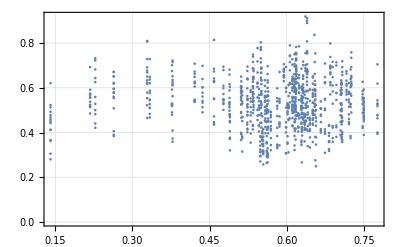

0.174901

```mathematica
(* evaluate performance on the test data: Plot label ejection fraction against the predicted EF *)
efp = ParallelMap[net[#]&,Keys@testDat];
efl = Values[testDat];
ListPlot[Transpose[{efl,efp}],
PlotRange->All,
GridLines->Automatic,
GridLinesStyle->Directive[Dotted, Gray],
Frame->True
]
RootMeanSquare[efl-efp]
```

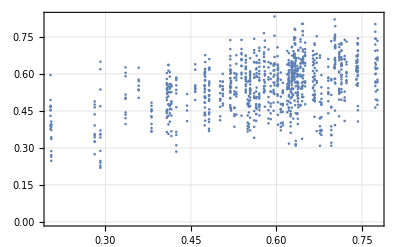

0.120814

```mathematica
(* just to compare with what looks like on the training data *)
efp = ParallelMap[net[#]&,Keys@trainDat];
efl = Values[trainDat];
ListPlot[Transpose[{efl,efp}],
PlotRange->All,
GridLines->Automatic,
GridLinesStyle->Directive[Dotted, Gray],
Frame->True
]
RootMeanSquare[efl-efp]
```

```mathematica
(* if continue to train can get very good perf on training data but always fails to generalize *)
```